```mathematica
Clear[initL,lambda]
initL[prgSymbol_,lambda1_]:=(
lambda[prgSymbol]^=lambda1;
);

Clear[callL,callt]
callL[prg_]:=(
-lambda[prg]Log[RandomReal[]]
)
s=Solve[-Sin[θ]^3/4+3Sin[θ]/4+1/2-r==0&&-Pi/2≤θ≤Pi/2,θ,Reals] //First//N  ;  (*на листочке получено интегрированием*)
callt[prgt_]:=(θ/.s/. r->RandomReal[])
```

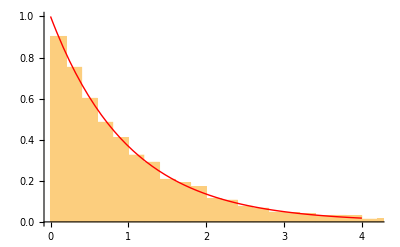

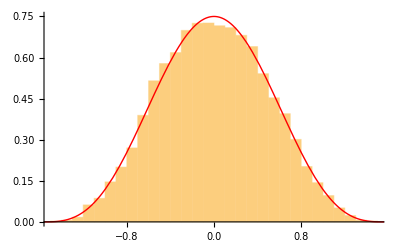

```mathematica
Clear[genTheta,genL]
initL[genL,1];
dataL = Table[callL[genL],{10000}];
dataTheta = Table[callt[genTheta],{10000}];
Show[Histogram[dataL,Automatic,"PDF"],Plot[Exp[-x],{x,0,4},PlotStyle->Directive[Red,Thick]]]
Show[Histogram[dataTheta,Automatic,"PDF"],Plot[3/4Cos[θ]^3,{θ,-Pi/2,Pi/2},PlotStyle->Directive[Red,Thick]]]
```

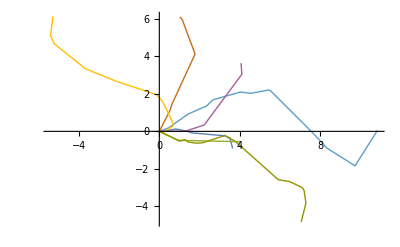

```mathematica
Clear[trajectory]
trajectory[p0_,genL_,genTheta_]:=Module[{p=p0},
lasttheta=0;
theta=0;
L=0;
track={{0,0}};
While[InverseCDF[BernoulliDistribution[1-p],RandomReal[]] == 1,
theta=callt[genTheta]+lasttheta;
L=callL[genL];
track=Append[track,Last[track]+{ L Cos[theta],L Sin[theta]}];
lasttheta=theta;
];
track
]
ListLinePlot[Table[trajectory[0.1,genL,genTheta],{10}],PlotStyle->Directive[Thick]]
```

```mathematica
(*функция усреднения прибавляет х из последнего элемент траектории/n измерений; потом график среднего х в зависимости от числа измерений*)
```

5.23728

7.72184+0.0012678 x

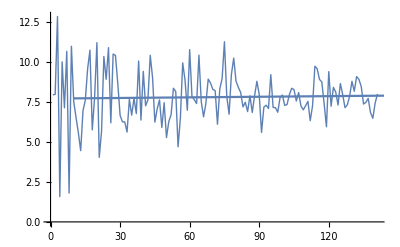

```mathematica
Clear[genL,averageX]
averageX[p0_,lambda0_,n0_]:=Module[{p=p0,n=n0,l=lambda0},
initL[genL,l];
AverageX =0;
For[i=1,i≤n,i++,
AverageX+=(trajectory[p,genL,genTheta]//Last//First)/n
];
AverageX
]
averageX[0.1,1,100]
fitdata=Table[averageX[0.1,2,n],{n,10,150}];
line=Fit[fitdata,{1,x},x]
Show[ListLinePlot[fitdata,PlotStyle->Directive[Thick]],Plot[line,{x,10,150}]]
```